## New

```mathematica
MM=3;NN=2;
(B=RandomInteger[{1,1000},{MM,NN}])//TableForm
B[[3,1]]
Log@N@Sum[B[[i,NN]]/Sum[B[[i,j]],{j,1,NN}],{i,1,MM}]
```

301 | 900
948 | 156
111 | 171

111

0.403505

```mathematica
DeltaS[m_,n_]:=Table[{B=RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]];
```

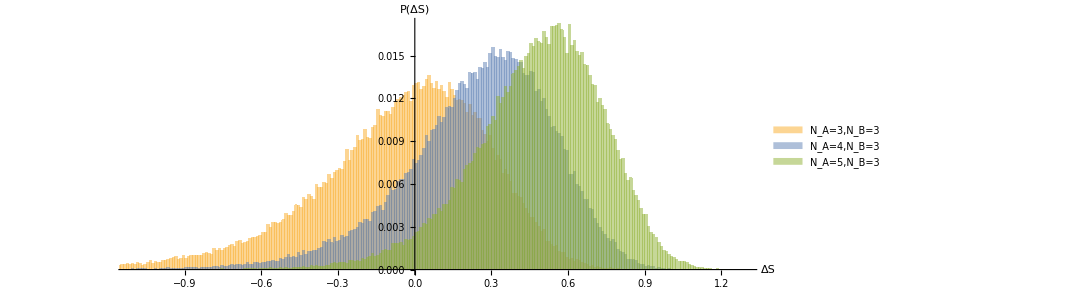

```mathematica
Histogram[{DeltaS[3,3],DeltaS[4,3],DeltaS[5,3]},{0.01},"Probability",AxesLabel->{Style["ΔS",FontSize->19, Bold,Background->White],Style["P(ΔS)",FontSize->18, Bold]},ImageSize->{800,300},AspectRatio->3/8, ChartLegends->{Style["N_A=3,N_B=3",FontSize->18, FontFamily->"Latin Modern Math"],Style["N_A=4,N_B=3",FontSize->18, FontFamily->"Latin Modern Math"],Style["N_A=5,N_B=3",FontSize->18, FontFamily->"Latin Modern Math"]},AxesOrigin->{0,0}]
```

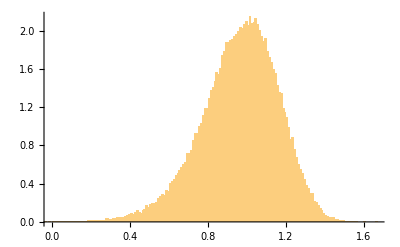

```mathematica
Histogram[DeltaS[8,3],{0.01},"PDF"]
```

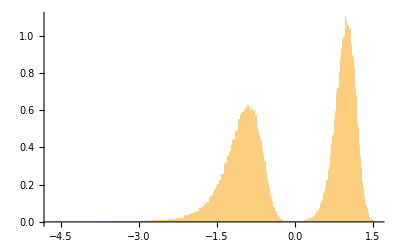

```mathematica
Histogram[Union[DeltaS[8,3],DeltaS[3,8]],{0.01},"PDF"]
```

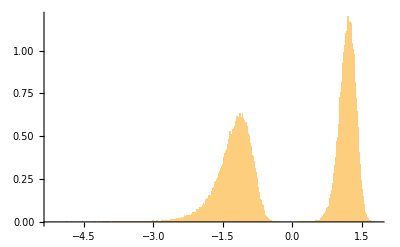

```mathematica
Histogram[Union[DeltaS[10,3],DeltaS[3,10]],{0.01},"PDF"]
```

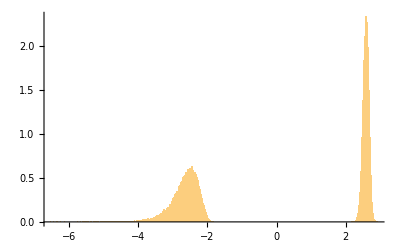

```mathematica
Histogram[Union[DeltaS[40,3],DeltaS[3,40]],{0.01},"PDF"]
```

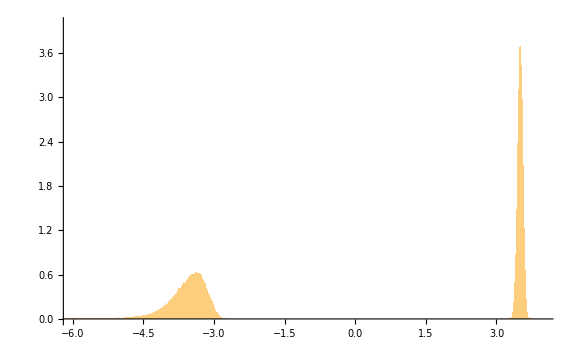

```mathematica
Histogram[Union[DeltaS[100,3],DeltaS[3,100]],{0.01},"PDF",PlotRange->{{-6,4},{0,4}},ImageSize->Large]
```

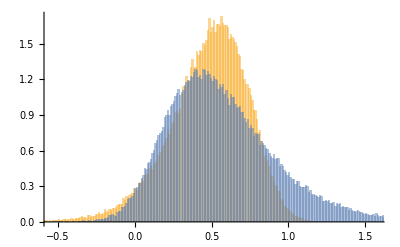

```mathematica
Histogram[{DeltaS[5,3],-DeltaS[3,5]},{0.01},"PDF"]
```

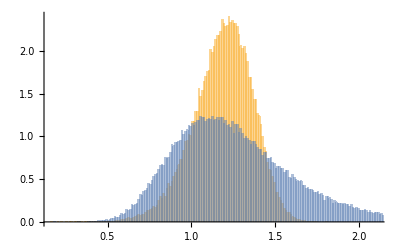

```mathematica
Histogram[{DeltaS[10,3],-DeltaS[3,10]},{0.01},"PDF"]
```

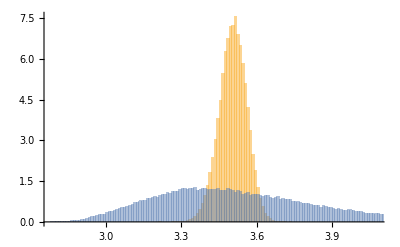

```mathematica
Histogram[{DeltaS[100,3],-DeltaS[3,100]},{0.01},"PDF"]
```

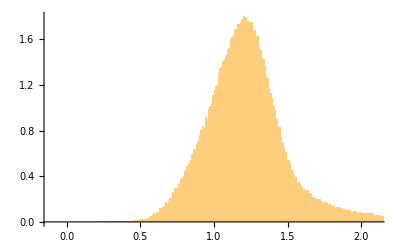

```mathematica
Histogram[Join[DeltaS[10,3],-DeltaS[3,10]],{0.01},"PDF"]
```

### Wigner

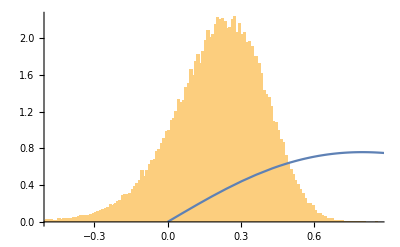

```mathematica
m=10;n=8;
Show[Histogram[Table[{B=RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"],Plot[π/2 s ⅇ^(-(π/4) s^2),{s,0,3}]]
```

```mathematica
m=.;n=.;
```

```mathematica
Show[Histogram[Table[{B=RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"],Plot[π/2 s ⅇ^(-(π/4) s^2),{s,0,3}]]/{m->2,n->10}
```

$Aborted

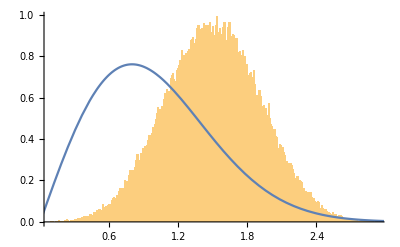

```mathematica
m=3;n=2;
Show[Histogram[Table[{B=RandomInteger[{1,1000},{m,n}],N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"],Plot[π/2 s ⅇ^(-(π/4) s^2),{s,0,3}]]
```

### Chi

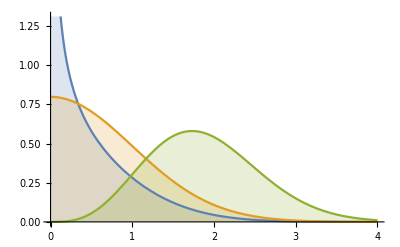

```mathematica
Plot[Table[PDF[ChiDistribution[ν],x],{ν,{.5,1,4}}]//Evaluate,{x,0,4},Filling->Axis]
```

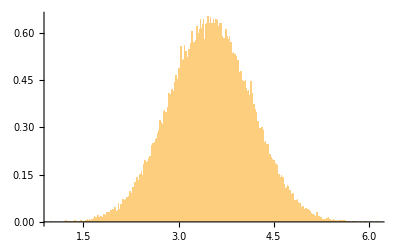

```mathematica
m=7;n=2;
Histogram[Table[{B=RandomInteger[{1,1000},{m,n}],N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"]
```

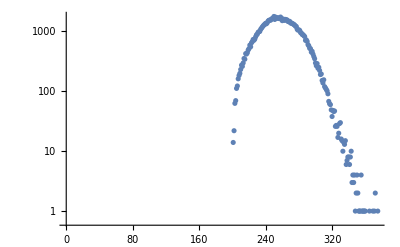

```mathematica
ListLogPlot[BinCounts[Table[{B=RandomInteger[{1,1000},{m,n}],N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{-1,1,0.005}]]
```

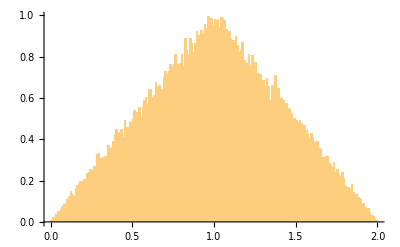

```mathematica
m=2;n=5;
Histogram[Normalize[Table[{B=RandomInteger[{1,1000},{m,n}],N@Sum[B[[i,n]],{i,1,m}]},{i,1,100000}][[;;,2]],Mean],{0.01},"PDF"]
```

### Maxwell

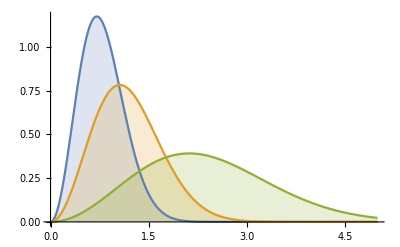

```mathematica
Plot[Table[PDF[MaxwellDistribution[σ],x],{σ,{.5,.75,1.5}}]//Evaluate,{x,0,5},Filling->Axis,PlotRange->All]
```

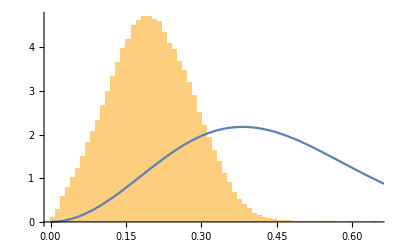

```mathematica
m=2;n=10;
Show[Histogram[Table[{B=RandomInteger[{1,1000},{m,n}],N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"],Plot[PDF[MaxwellDistribution[0.27],x],{x,0,4},PlotRange->Full]]
```

### Poisson

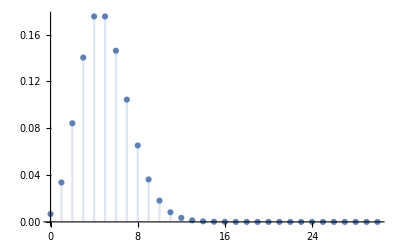

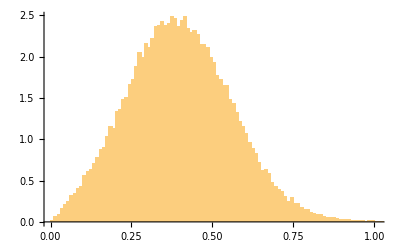

```mathematica
m=2;n=5;
Histogram[Table[{B=RandomInteger[{1,1000},{m,n}],N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"]
```

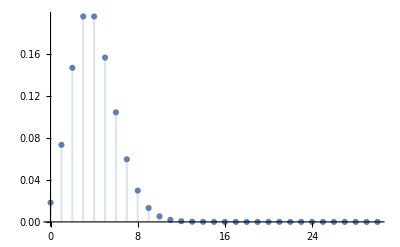

```mathematica
DiscretePlot[PDF[PoissonDistribution[4],k]//Evaluate,{k,0,30}]
```

### Other

```mathematica
A=Table[{B=-RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,10}][[;;,2]]
```

{-1.59218,-1.26337,-0.959079,-0.990702,-0.991615,-1.04692,-0.853468,-1.21013,-1.53396,-1.0937}

```mathematica
Normalize[-A,Mean]
```

{1.38029,1.09524,0.831442,0.858857,0.859648,0.907595,0.739885,1.04908,1.32982,0.94815}

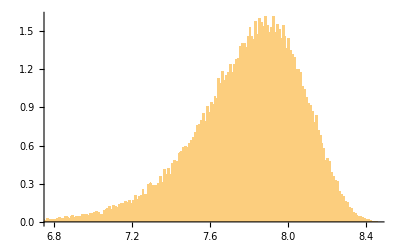

```mathematica
m=5;n=10;
Histogram[Table[{B=RandomInteger[{0,1000},{m,n}],Log@N@Sum[B[[i,1]],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"]
```

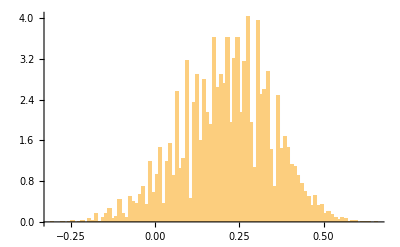

```mathematica
m=5;n=4;
Histogram[Table[{B=Round[RandomReal[{1,2},{m,n}]],Log@N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"]
```

## Poisson New

```mathematica
DeltaS[m_,n_]:=Table[{B=Table[RandomVariate[PoissonDistribution[20],n],m],Log@N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]];
```

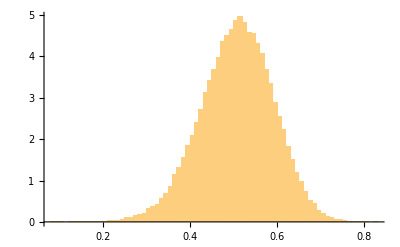

```mathematica
Histogram[DeltaS[5,3],{0.01},"PDF"]
```

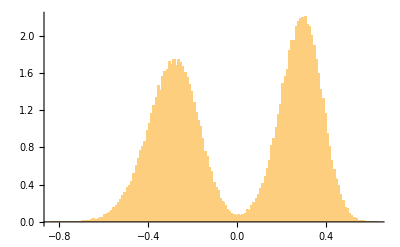

```mathematica
Histogram[Union[DeltaS[4,3],DeltaS[3,4]],{0.01},"PDF"]
```

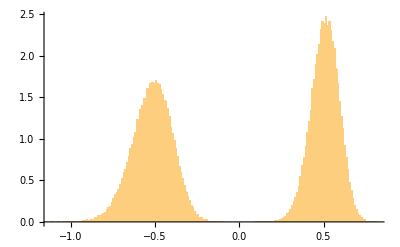

```mathematica
Histogram[Union[DeltaS[5,3],DeltaS[3,5]],{0.01},"PDF"]
```

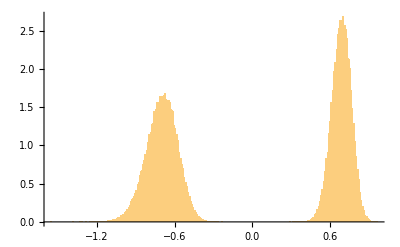

```mathematica
Histogram[Union[DeltaS[6,3],DeltaS[3,6]],{0.01},"PDF"]
```

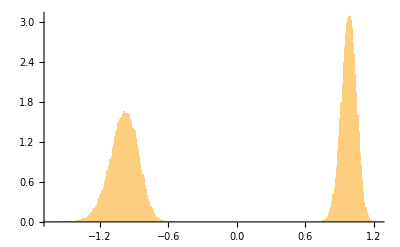

```mathematica
Histogram[Union[DeltaS[8,3],DeltaS[3,8]],{0.01},"PDF"]
```

### Wigner

```mathematica
m=10;n=8;
Show[Histogram[Table[{B=RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"],Plot[π/2 s ⅇ^(-(π/4) s^2),{s,0,3}]]
```

-Graphics-

```mathematica
m=.;n=.;
```

```mathematica
Show[Histogram[Table[{B=RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"],Plot[π/2 s ⅇ^(-(π/4) s^2),{s,0,3}]]/{m->2,n->10}
```

$Aborted

```mathematica
m=3;n=2;
Show[Histogram[Table[{B=RandomInteger[{1,1000},{m,n}],N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"],Plot[π/2 s ⅇ^(-(π/4) s^2),{s,0,3}]]
```

-Graphics-

### Chi

```mathematica
Plot[Table[PDF[ChiDistribution[ν],x],{ν,{.5,1,4}}]//Evaluate,{x,0,4},Filling->Axis]
```

-Graphics-

```mathematica
m=7;n=2;
Histogram[Table[{B=RandomInteger[{1,1000},{m,n}],N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"]
```

-Graphics-

```mathematica
ListLogPlot[BinCounts[Table[{B=RandomInteger[{1,1000},{m,n}],N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{-1,1,0.005}]]
```

-Graphics-

```mathematica
m=2;n=5;
Histogram[Normalize[Table[{B=RandomInteger[{1,1000},{m,n}],N@Sum[B[[i,n]],{i,1,m}]},{i,1,100000}][[;;,2]],Mean],{0.01},"PDF"]
```

-Graphics-

### Maxwell

```mathematica
Plot[Table[PDF[MaxwellDistribution[σ],x],{σ,{.5,.75,1.5}}]//Evaluate,{x,0,5},Filling->Axis,PlotRange->All]
```

-Graphics-

```mathematica
m=2;n=10;
Show[Histogram[Table[{B=RandomInteger[{1,1000},{m,n}],N@Sum[B[[i,1]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"],Plot[PDF[MaxwellDistribution[0.27],x],{x,0,4},PlotRange->Full]]
```

-Graphics-

### Poisson

-Graphics-

```mathematica
m=2;n=5;
Histogram[Table[{B=RandomInteger[{1,1000},{m,n}],N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"]
```

-Graphics-

```mathematica
DiscretePlot[PDF[PoissonDistribution[4],k]//Evaluate,{k,0,30}]
```

-Graphics-

### Other

```mathematica
A=Table[{B=-RandomInteger[{1,1000},{m,n}],Log@N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,10}][[;;,2]]
```

{-1.59218,-1.26337,-0.959079,-0.990702,-0.991615,-1.04692,-0.853468,-1.21013,-1.53396,-1.0937}

```mathematica
Normalize[-A,Mean]
```

{1.38029,1.09524,0.831442,0.858857,0.859648,0.907595,0.739885,1.04908,1.32982,0.94815}

```mathematica
m=5;n=10;
Histogram[Table[{B=RandomInteger[{0,1000},{m,n}],Log@N@Sum[B[[i,1]],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"]
```

-Graphics-

```mathematica
m=5;n=4;
Histogram[Table[{B=Round[RandomReal[{1,2},{m,n}]],Log@N@Sum[B[[i,n]]/Sum[B[[i,j]],{j,1,n}],{i,1,m}]},{i,1,100000}][[;;,2]],{0.01},"PDF"]
```

-Graphics-

## Old

# Orthogonal

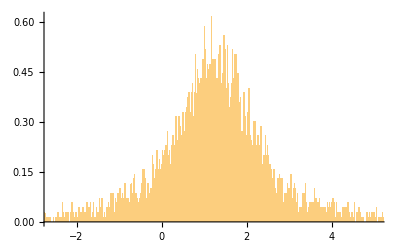

```mathematica
initial =2;
final =2;
Histogram[Table[Log@Sum[(A=Table[RandomVariate[GaussianOrthogonalMatrixDistribution[final]][[1]],{i,1,initial}])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

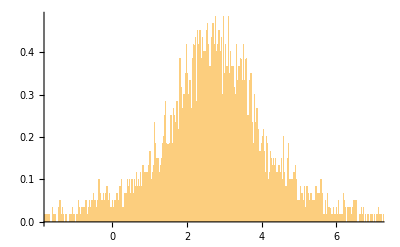

$Aborted

```mathematica
initial =5;
final =3;
Histogram[Table[Log@Sum[(A=Table[RandomVariate[GaussianOrthogonalMatrixDistribution[final]][[1]],{i,1,initial}])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
$Aborted
```

```mathematica
A=Table[RandomVariate[GaussianOrthogonalMatrixDistribution[final]][[1]],{i,1,initial}]//MatrixForm
```

(0.460502 | 0.365167 | 0.678814
-2.6077 | -0.618653 | 0.065228
0.286064 | -0.0609491 | -0.250816
-0.276895 | 0.34143 | -0.787715
-0.301292 | -0.316751 | -0.451454)

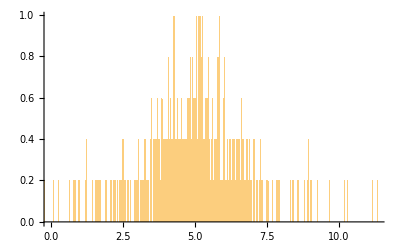

```mathematica
initial =10;
final =10;
Histogram[Table[Log@Sum[(A=Table[RandomVariate[GaussianOrthogonalMatrixDistribution[final]][[1]],{i,1,initial}])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,1000}],{0.01},"PDF"]
```

## Circular

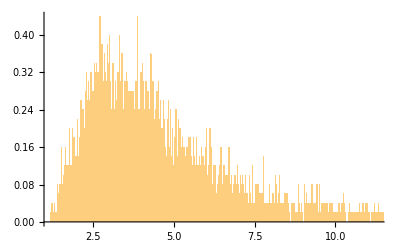

```mathematica
size=3;
Histogram[Table[Log@Sum[(A=RandomVariate[CircularRealMatrixDistribution[size]]^2)[[k,1]]/A[[k,m]],{k,1,Length@A},{m,1,Length@A}],{i,1,5000}],{0.01},"PDF"]
```

## Non-circular

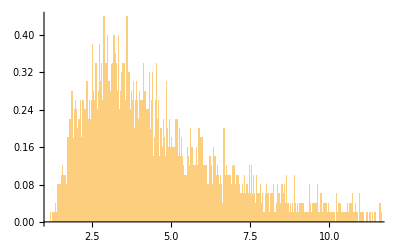

```mathematica
size=3;
Histogram[Table[Log@Sum[(A=Table[RandomVariate[CircularRealMatrixDistribution[size]][[i]],{i,1,size}]^2)[[k,1]]/A[[k,m]],{k,1,Length@A},{m,1,Length@A}],{i,1,5000}],{0.01},"PDF"]
```

## Non-square non-circular

To pierwsze jest poprawne, prawdopodobieństwa stanów początkowych są znormalizowane

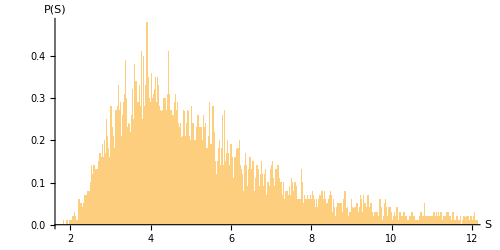

```mathematica
initial =5;
final =3;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF", AxesLabel->{Style["S",FontSize->16, Bold],Style["P(S)",FontSize->16, Bold]},ImageSize->{500,250},AspectRatio->1/2]
```

```mathematica
A=(Table[RandomVariate[CircularRealMatrixDistribution[final]][[1]],{i,1,initial}]^2);
```

```mathematica
A//TableForm
```

0.275776 | 0.126615 | 0.0942106 | 0.00376612 | 0.499631
0.130464 | 0.00727425 | 0.36795 | 0.30108 | 0.193231

```mathematica
Sum[A[[1,m]],{m,1,final}]
```

1.

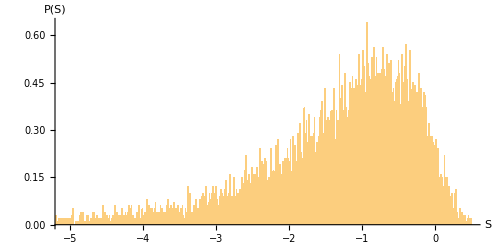

```mathematica
initial =2;
final =5;
Histogram[Table[Log@Sum[(A=Table[RandomVariate[CircularRealMatrixDistribution[final]][[1]],{i,1,initial}]^2)[[k,1]]/Sum[A[[k,m]],{m,1,final}],{k,1,initial}],{i,1,10000}],{0.01},"PDF", AxesLabel->{Style["S",FontSize->16, Bold],Style["P(S)",FontSize->16, Bold]},ImageSize->{500,250},AspectRatio->1/2]
```

.

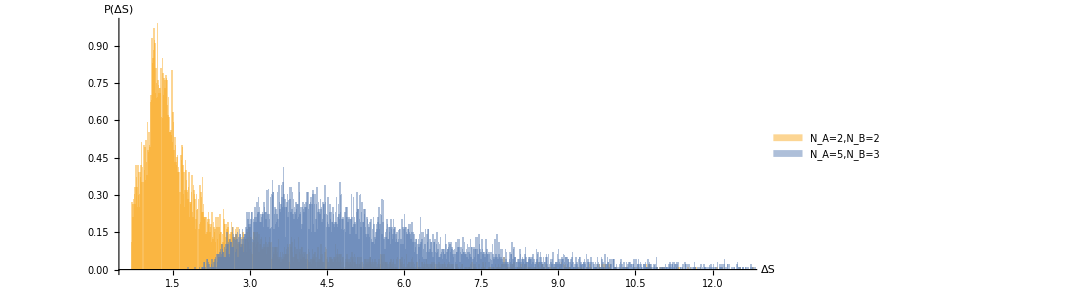

```mathematica
Histogram[{Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[2]][[1]],{i,1,2}]^2])[[k,1]]/A[[k,m]],{k,1,2},{m,1,2}],{i,1,10000}],Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[5]][[1]],{i,1,3}]^2])[[k,1]]/A[[k,m]],{k,1,5},{m,1,3}],{i,1,10000}]},{0.01},"PDF", AxesLabel->{Style["ΔS",FontSize->19, Bold,Background->White],Style["P(ΔS)",FontSize->18, Bold]},ImageSize->{800,300},AspectRatio->3/8, ChartLegends->{Style["N_A=2,N_B=2",FontSize->18, FontFamily->"Latin Modern Math"],Style["N_A=5,N_B=3",FontSize->18, FontFamily->"Latin Modern Math"]},PlotRangePadding->{0.7,Automatic}]
```

A nie prawdopodobieństwa stanów końcowych, jak poniżej

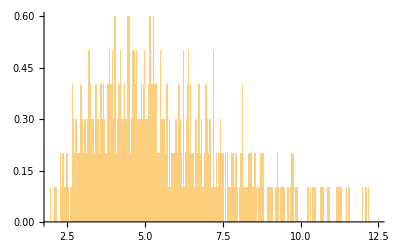

```mathematica
initial =5;
final =3;
Histogram[Table[Log@Sum[(A=Table[RandomVariate[CircularRealMatrixDistribution[final]][[1]]^2,{i,1,initial}]^2)[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,1000}],{0.01},"PDF"]
```

# Weźmy jeszcze więcej stanów początkowych

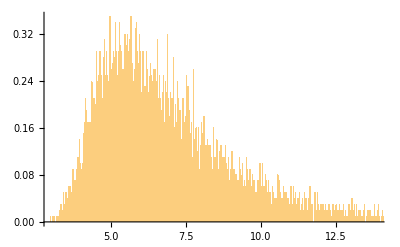

```mathematica
initial =10;
final =3;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

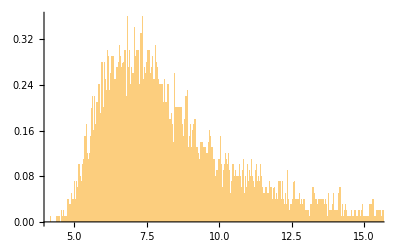

```mathematica
initial =20;
final =3;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

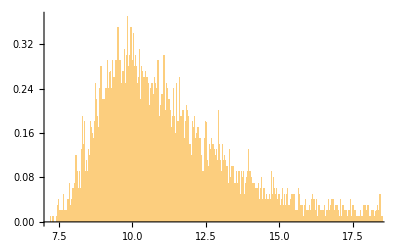

```mathematica
initial =20;
final =10;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

```mathematica
A=RandomVariate[CircularRealMatrixDistribution[3]]
```

{{0.509165,-0.818874,0.264944},{0.422529,0.506012,0.751945},{-0.749813,-0.270918,0.603642}}

```mathematica
Total[A^2]
```

{1.,1.,1.}

```mathematica
A
```

{{0.509165,-0.818874,0.264944},{0.422529,0.506012,0.751945},{-0.749813,-0.270918,0.603642}}

```mathematica
A[[1]]^2
```

{0.259249,0.670555,0.0701955}

# Testing it out

# 1->2 or 1->3 probability

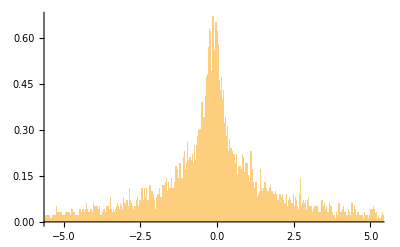

```mathematica
initial =2;
final =2;
Histogram[Table[Log@(Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}]/Sum[A[[k,2]]/A[[k,m]],{k,1,initial},{m,1,final}]),{i,1,10000}],{0.01},"PDF"]
```

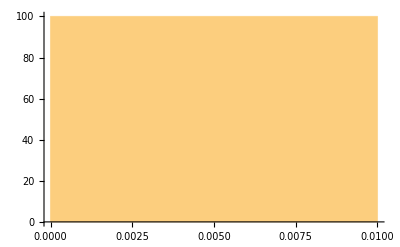

```mathematica
initial =1;
final =1;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

```mathematica
sample=RandomVariate[NormalDistribution[2,3],10^3];
```

## Free energy? probably not

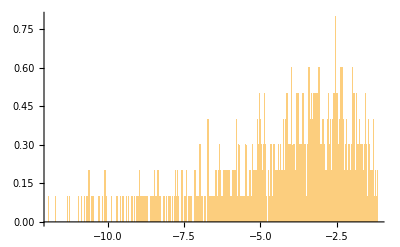

```mathematica
initial =2;
final =2;
Histogram[Table[-Log@ Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]]/A[[1,1]],{k,1,initial},{m,1,final}],{i,1,1000}],{0.01},"PDF"]
```